```mathematica
PGamma[0,p_]:=1;
PGamma[n_,p_]:=PGamma[n,p]=If[Mod[n,p]==0,-1*PGamma[n-1,p],-n*PGamma[n-1,p]];
```

```mathematica
PochGamma[n_,m_,p_]:=Product[If[Mod[k,p]==0,1,k],{k,n,n+m-1}]
```

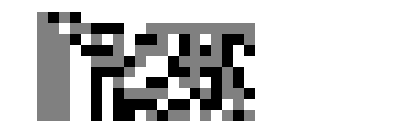

```mathematica
Module[{p=3,c=1},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[PochGamma[c*p^n+1,c*p^n,p]/Product[PGamma[c*p^i,p],{i,0,n}],p^20],p,30]],{n,1,10}]]]
```

```mathematica
L = Table[Reverse[IntegerDigits[Abs[PGamma[3^n,3]],3,30]],{n,1,15}]
```

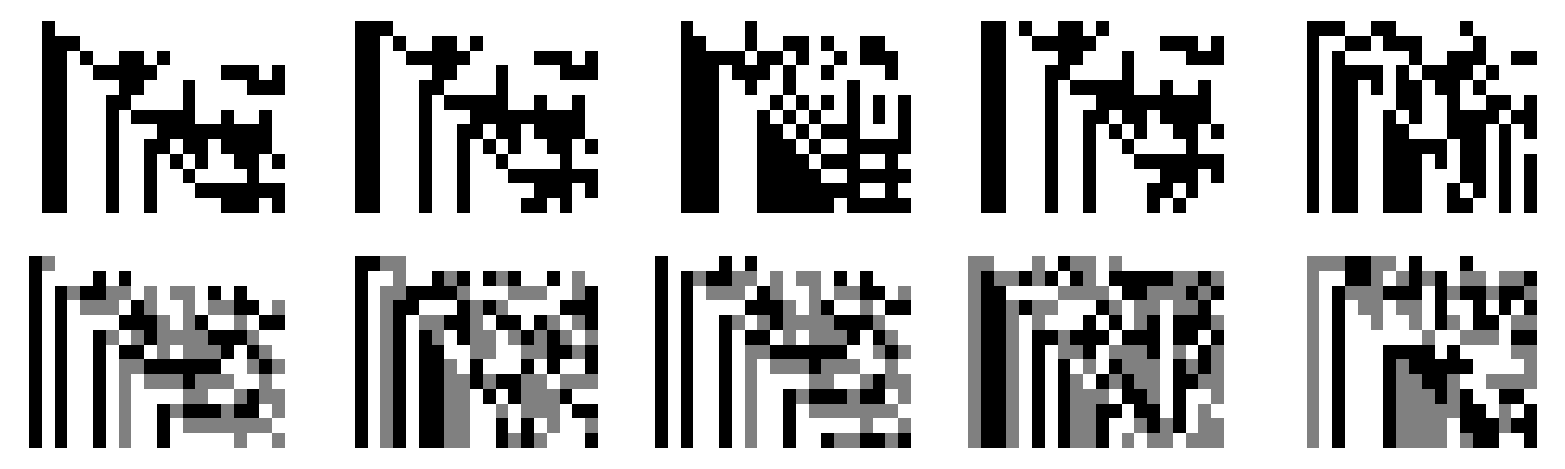

```mathematica
Grid[Table[ArrayPlot[Table[Reverse[IntegerDigits[CatalanNumber[a*p^n],p,20]],{n,1,13}]],{p,2,3},{a,1,5}]]
```

```mathematica
ArrayPlot[L]
```

-Graphics-

```mathematica
L = Table[Reverse[IntegerDigits[Abs[PGamma[3^n,3]]+1,3,30]],{n,2,15}]
```

{{0,0,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,2,2,1,0,1,0,0,0,1,1,0,2,0,0,2,2,1,2,0,1,0,2,0,2,0,1},{0,0,0,0,0,2,2,1,2,1,1,2,2,1,0,1,2,2,2,0,2,1,2,2,0,0,1,0,2,0},{0,0,0,0,0,0,2,2,1,2,1,2,0,2,2,1,1,2,0,2,2,0,1,2,1,2,1,1,0,2},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,2,2,2,2,0,1,1,1,1,0,1,1,1,0,1},{0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,1,2,0,1,1,0,0,0,2,0,2,1,2,1},{0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,2,1,2,2,0,2,0,2,0,1,0,2},{0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,1,0,2,2,2,2,2,2,2,0},{0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,0,0,2,2,0,2,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,2,2,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,1,2,2,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,1,1}}

```mathematica
L = Table[Reverse[IntegerDigits[(Abs[PGamma[3^n,3]]+1)/3^n,3,30]],{n,2,15}]
```

{{0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,2,1,0,1,0,0,0,1,1,0,2,0,0,2,2,1,2,0,1,0,2,0,2,0,1,0,2,0},{0,2,2,1,2,1,1,2,2,1,0,1,2,2,2,0,2,1,2,2,0,0,1,0,2,0,1,0,1,0},{0,2,2,1,2,1,2,0,2,2,1,1,2,0,2,2,0,1,2,1,2,1,1,0,2,1,0,0,0,1},{0,2,2,1,2,1,2,2,0,2,2,2,2,0,1,1,1,1,0,1,1,1,0,1,0,2,2,0,1,1},{0,2,2,1,2,1,2,2,2,1,2,0,1,1,0,0,0,2,0,2,1,2,1,0,2,0,2,2,1,0},{0,2,2,1,2,1,2,2,2,0,2,1,2,2,0,2,0,2,0,1,0,2,2,1,2,1,2,2,0,2},{0,2,2,1,2,1,2,2,2,0,1,1,0,2,2,2,2,2,2,2,0,2,1,2,2,1,1,0,2,1},{0,2,2,1,2,1,2,2,2,0,1,0,0,0,2,2,0,2,0,2,1,1,0,2,2,0,1,1,0,1},{0,2,2,1,2,1,2,2,2,0,1,0,2,2,2,1,0,1,0,0,1,2,1,2,0,1,1,2,2,1},{0,2,2,1,2,1,2,2,2,0,1,0,2,1,2,2,2,0,2,0,2,1,2,0,0,1,0,0,2,1},{0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,2,0,0,2,2,2,0,2,1,1,0,2,0,1,1},{0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,1,0,1,1,2,1,1,1,2,2,1,1,2,0,2},{0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,1,2,0,2,1,1,0,2,1,0,1,0,2,2,1}}

```mathematica
ArrayPlot[L]
```

-Graphics-

```mathematica
L2 = Table[Reverse[IntegerDigits[CatalanNumber[2^n],2,30]],{n,2,15}]
```

{{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,1,1,1,0,0,0,0,0,1,1,1,0,1,1,0,0,0,0,1,0,0,0,0},{0,1,1,0,0,0,0,1,1,0,0,0,1,0,0,0,0,1,1,1,0,1,1,1,1,0,0,0,1,0},{0,1,1,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,1,1},{0,1,1,0,0,0,1,0,1,1,1,1,1,0,0,1,0,0,1,0,0,1,1,0,1,1,0,1,1,0},{0,1,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,0,1,1,1,0,0},{0,1,1,0,0,0,1,0,0,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,1,1},{0,1,1,0,0,0,1,0,0,1,0,1,0,1,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,1},{0,1,1,0,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1},{0,1,1,0,0,0,1,0,0,1,0,0,0,1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,1,1,1,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,1,1,0,1,1,0,1}}

```mathematica
ArrayPlot[L2]
```

-Graphics-

```mathematica
L3 = Table[Reverse[IntegerDigits[PGamma[2^(n+1)+1,2]/Product[PGamma[2^(n-k)+1,2],{k,0,n}],2,30]],{n,2,15}];
```

```mathematica
L4 = Table[Reverse[IntegerDigits[PolynomialMod[((-1)^(n+1)*Product[PGamma[2^(n+1-k)+1,2],{k,0,n+1}])/Product[PGamma[2^(n-k)+1,2]^2,{k,0,n}],2^30],2,30]],{n,2,15}]
```

{{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,1,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,1,1,0,0,0,0,1,1,0,1,0,1},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,1,0,1,1},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,0,1,0,0,0,0,1,0,1,1,0,0,0,0},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,1},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0,1,1,0,0,1,0,0,0,0,1,0},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,1,0,1,1,0,0,0,1},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,0,1,1,1,0,1},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,0},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,1,0,1,0,0,0},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,1,0,1,0,1,1},{1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,1,0,1,0,1,1}}

```mathematica
ArrayPlot[L4]
```

-Graphics-

```mathematica
L5 = Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[2^n],2^30],2,30]],{n,2,15}]
```

{{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,1,1,1,0,0,0,0,0,1,1,1,0,1,1,0,0,0,0,1,0,0,0,0},{0,1,1,0,0,0,0,1,1,0,0,0,1,0,0,0,0,1,1,1,0,1,1,1,1,0,0,0,1,0},{0,1,1,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,1,1},{0,1,1,0,0,0,1,0,1,1,1,1,1,0,0,1,0,0,1,0,0,1,1,0,1,1,0,1,1,0},{0,1,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,0,1,1,1,0,0},{0,1,1,0,0,0,1,0,0,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,1,1},{0,1,1,0,0,0,1,0,0,1,0,1,0,1,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,1},{0,1,1,0,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1},{0,1,1,0,0,0,1,0,0,1,0,0,0,1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,1,1,1,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,1,1,0,1,1,0,1}}

```mathematica
ArrayPlot[L5]
```

-Graphics-

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[PGamma[2^n,2],2^30],2,30]],{n,2,15}]]
```

-Graphics-

```mathematica
Valuation[n_,p_]:=IntegerExponent[Numerator[n],p]-IntegerExponent[Denominator[n],p]
```

```mathematica
SetAttributes[Valuation,Listable]
```

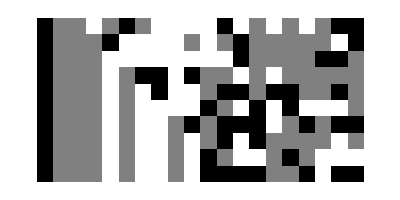

```mathematica
Module[{p=3,a=5,digits=20,rows=10},L=Table[Reverse[IntegerDigits[PolynomialMod[Product[PGamma[2a*p^i,p]/PGamma[a*p^i,p],{i,0,n}],p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L]]
```

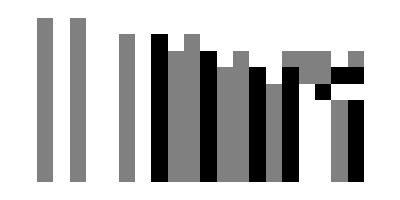

```mathematica
Module[{p=3,a=1,digits=20,rows=10},L=Table[Reverse[IntegerDigits[PolynomialMod[Product[PGamma[2a*p^i,p]/(PGamma[a*p^i,p]^2),{i,0,n}],p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L]]
```

```mathematica
PFact[n_,p_]:=n!/(p^((n-Total[IntegerDigits[n,p]])/(p-1)))
```

```mathematica
Lambda[a_,p_]:=Module[{q=Floor[a/p],r=Mod[a,p]},If[r==0,PFact[q,p],a*PFact[q,p]]]
```

```mathematica
Lambda2[a_,p_]:=Module[{q=Floor[a/p],r=Mod[a,p]},If[r==0,q!,a*q!]]
```

```mathematica
Gambda[a_,p_]:=Lambda[2a,p]/((Lambda[a,p])^2)
```

```mathematica
Gambda2[a_,p_]:=Lambda2[2a,p]/((Lambda2[a,p])^2)
```

```mathematica
ExponentThing[a_,p_]:=p^(2Total[IntegerDigits[a,p]]-Total[IntegerDigits[2a,p]])
```

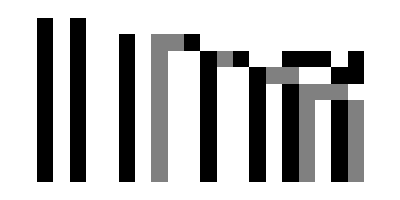

```mathematica
Module[{p=3,a=1,digits=20,rows=10},L3=Table[Reverse[IntegerDigits[PolynomialMod[ExponentThing[a,p]*Gambda[a,p]*Product[PGamma[2a*p^i,p]/(PGamma[a*p^i,p]^2),{i,0,n}],p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L3]]
```

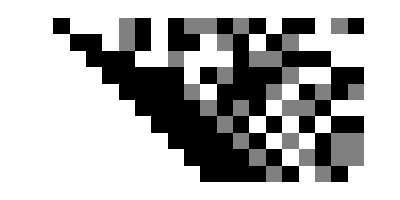

```mathematica
Module[{p=3,a=13,digits=20,rows=10},L3=Table[Reverse[IntegerDigits[PolynomialMod[ExponentThing[a,p]*Gambda[a,p]*Product[PGamma[2a*p^i,p]/(PGamma[a*p^i,p]^2),{i,0,n}]-CatalanNumber[a*p^n],p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L3]]
```

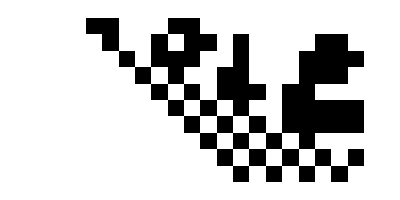

```mathematica
Module[{p=2,a=3,digits=20,rows=10},L3=Table[Reverse[IntegerDigits[PolynomialMod[ExponentThing[a,p]*Gambda[a,p]*Product[Abs[PGamma[2a*p^i,p]]/(PGamma[a*p^i,p]^2),{i,0,n}]-CatalanNumber[a*p^n],p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L3]]
```

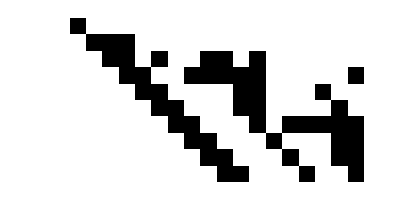
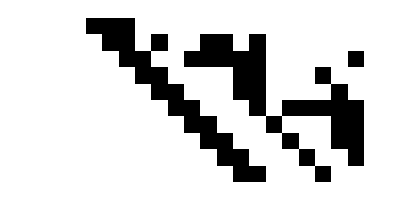
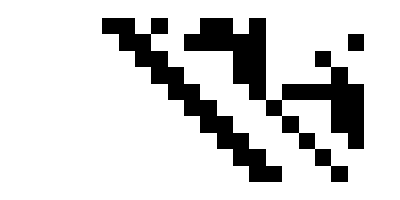
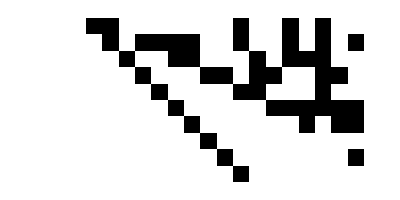
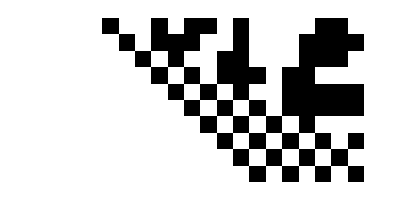
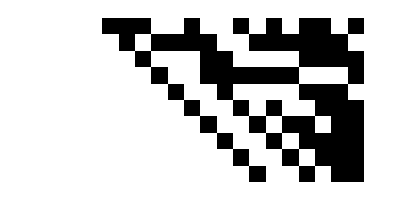
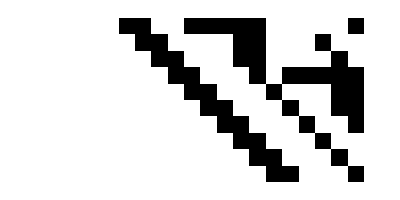
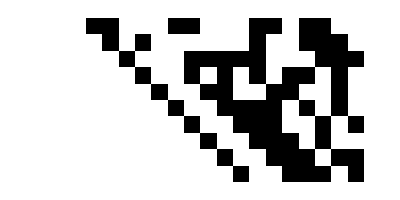
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Module[{p=2,digits=20,rows=10},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[ExponentThing[a,p]*Gambda[a,p]*Product[Abs[PGamma[2a*p^i,p]]/(PGamma[a*p^i,p]^2),{i,0,n}]-CatalanNumber[a*p^n],p^digits],p,digits]],{n,1,rows}]]],{a,1,20}]
```

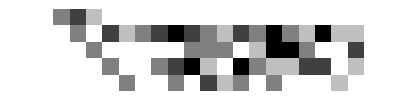
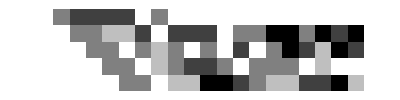
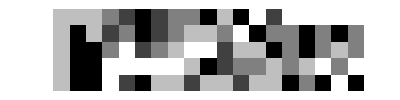
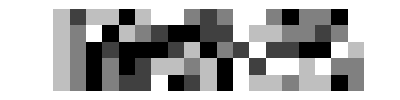
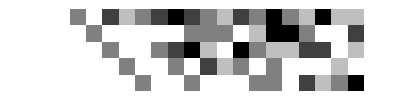
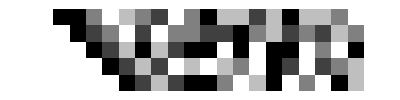
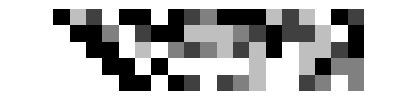
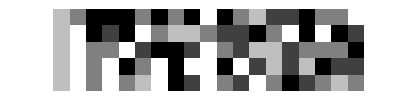

```mathematica
Table[Module[{p=5,digits=20,rows=5},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[ExponentThing[a,p]*Gambda[a,p]*Product[PGamma[2*a*p^i,p]/(PGamma[a*p^i,p]^2),{i,0,n}]-CatalanNumber[a*p^n],p^digits],p,digits]],{n,1,rows}]]],{a,1,10}]
```

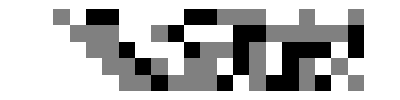
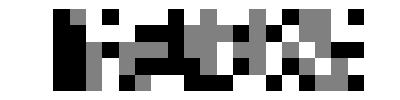
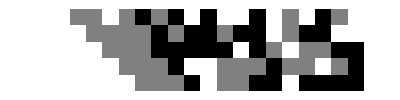
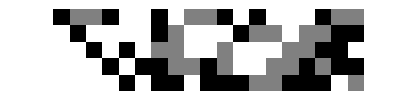
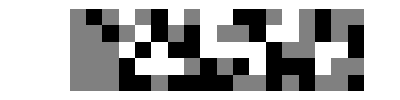
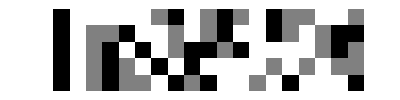
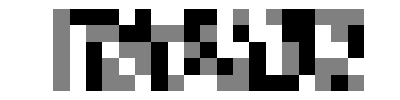
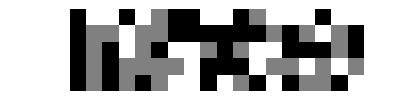

```mathematica
Table[Module[{p=3,digits=20,rows=5},ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[ExponentThing[a,p]*Gambda[a,p]*Product[PGamma[2*a*p^i,p]/(PGamma[a*p^i,p]^2),{i,0,n}]-CatalanNumber[a*p^n],p^digits],p,digits]],{n,1,rows}]]],{a,28,56}]
```

```mathematica
ExponentThing[4,3]
```

1

```mathematica
Table[Lambda[2n,3]/(Lambda[n,3]^2),{n,0,20}]
```

{1,2,1,2,1,4/5,2,4/7,5/2,20,4,280/11,70,140/13,10,28,7/2,616/17,308,616/19,2002/5}

```mathematica
Table[Lambda[2n,5]/(Lambda[n,5]^2),{n,0,20}]
```

{1,2,1,2/3,1/2,2,2/3,4/7,3/2,4/3,6,12/11,1,12/13,6/7,4,1/2,8/17,28/9,56/19,14}

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[Lambda[2n,2]/(Lambda[n,2]^2),2^20],2,20]],{n,0,20}]]
```

-Graphics-

```mathematica
Module[{p=3,digits=5},Table[Table[PolynomialMod[(ExponentThing[a,p]*Product[PGamma[2a*p^i,p]/PGamma[a*p^i,p],{i,0,n}])/CatalanNumber[a*p^n],p^digits],{n,1,10}],{a,1,10}]]
```

{{4,199,55,109,28,28,28,28,28,28},{111,12,201,39,39,39,39,39,39,39},{44,188,134,215,215,215,215,215,215,215},{191,230,104,212,50,50,50,50,50,50},{234,126,45,45,45,45,45,45,45,45},{6,222,141,141,141,141,141,141,141,141},{6,69,15,96,96,96,96,96,96,96},{36,144,225,225,225,225,225,225,225,225},{185,212,50,50,50,50,50,50,50,50},{29,113,122,149,230,230,230,230,230,230}}

```mathematica
Module[{p=3,digits=5},Table[Table[PolynomialMod[(ExponentThing[a,p]*Product[1/PGamma[a*p^i,p],{i,0,n}]^(a))/CatalanNumber[a*p^n],p^digits],{n,1,10}],{a,1,10}]]
```

{{73,196,79,214,133,133,133,133,133,133},{177,6,222,141,141,141,141,141,141,141},{5,14,41,122,122,122,122,122,122,122},{229,226,217,190,109,109,109,109,109,109},{9,117,198,198,198,198,198,198,198,198},{15,69,231,231,231,231,231,231,231,231},{150,186,51,132,132,132,132,132,132,132},{72,45,207,207,207,207,207,207,207,207},{50,77,158,158,158,158,158,158,158,158},{202,208,226,37,199,199,199,199,199,199}}

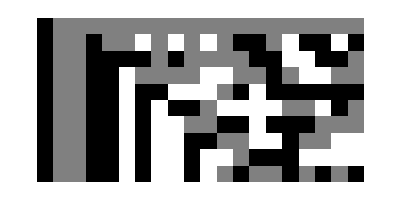
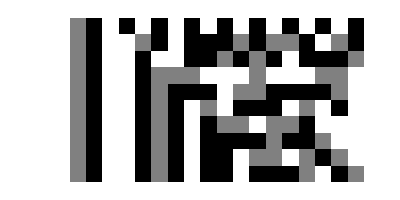
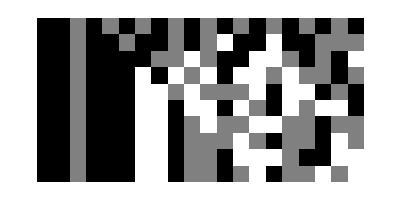
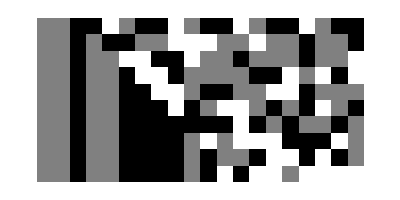
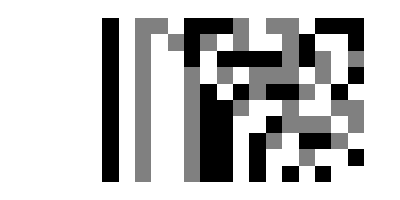
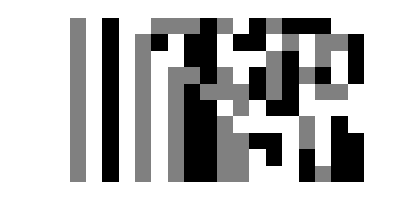
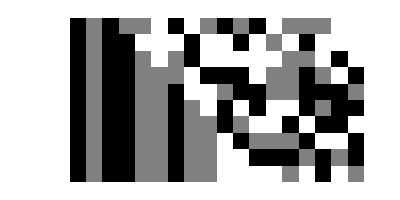
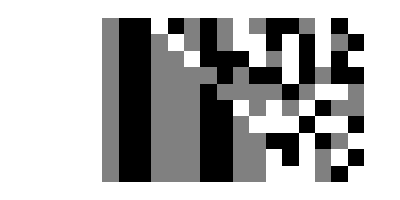

```mathematica
Module[{p=3,digits=20},Table[ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[ExponentThing[a,p]*Product[1/PGamma[p^i,p],{i,0,n}]^(a),p^digits],p,digits]],{n,1,10}]],{a,1,10}]]
```

```mathematica
Module[{p=3,digits=20},Table[ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[ExponentThing[a,p]*Product[1/PGamma[p^i,p],{i,0,n}]^(a),p^digits],p,digits]],{n,1,10}]],{a,1,10}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

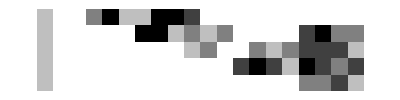

```mathematica
Module[{p=5,a=3,digits=20,rows=5},L30=Table[Reverse[IntegerDigits[PolynomialMod[(PGamma[2a*p^n,p]^(n))/(PGamma[a*p^n,p]^(2n)),p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L30]]
```

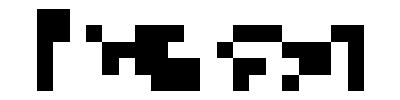

```mathematica
Module[{p=2,a=1,digits=20,rows=5},L30=Table[Reverse[IntegerDigits[PolynomialMod[(PGamma[2a*p^n,p]^(n))/(Product[
If[Mod[i,p]==0,1,i^(Floor[Log[p,i/(2a)]])],
{i,a*p^n+1,2a*p^n-1}]PGamma[a*p^n,p]^(2n)),p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L30]]
```

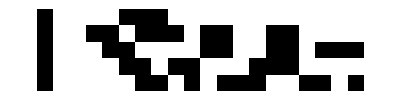

```mathematica
Module[{p=2,a=3,digits=20,rows=5},L30=Table[Reverse[IntegerDigits[PolynomialMod[PGamma[a*p^n,p]^(2),p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L30]]
```

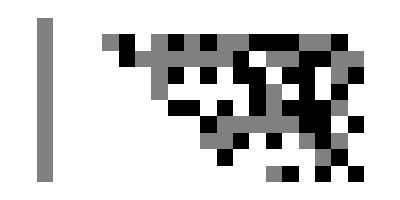

```mathematica
Module[{p=3,a=6,digits=20,rows=10},
L30=Table[
Reverse[
IntegerDigits[
PolynomialMod[
Product[
If[Mod[i,p]==0,1,i^(-Floor[Log[p,i/(2a)]])],
{i,a*p^n+1,2a*p^n-1}]
,p^digits],p,digits]
],
{n,1,rows}];
ArrayPlot[L30]]
```

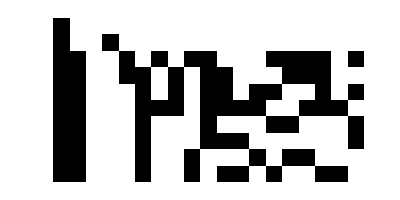

```mathematica
Module[{p=2,a=1,digits=20,rows=10},
L30=Table[
Reverse[
IntegerDigits[
PolynomialMod[
((2a)!)/(a!)^2 Product[
If[Mod[i,p]==0,1,i^(Floor[Log[p,i/(a)]]+1)],
{i,1,a*p^n-1}]
,p^digits],p,digits]
],
{n,1,rows}];
ArrayPlot[L30]]
```

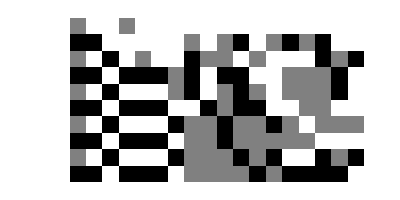

```mathematica
Module[{p=3,a=5,digits=20,rows=10},
L30=Table[
Reverse[
IntegerDigits[
PolynomialMod[
((2a)!)/(a!)^2 Product[
If[Mod[i,p]==0,1,i^(2Floor[Log[p,i/(a)]]-Floor[Log[p,i/(2a)]])],
{i,a*p+1,a*p^n-1}]
,p^digits],p,digits]
],
{n,1,rows}];
ArrayPlot[L30]]
```

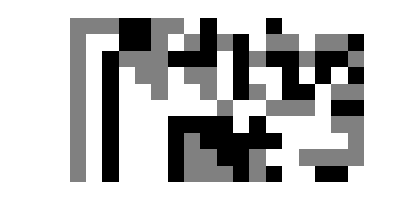

```mathematica
Module[{p=3,a=5,digits=20,rows=10},
L31=Table[
Reverse[
IntegerDigits[
PolynomialMod[
CatalanNumber[a*p^n],p^digits],p,digits]
],
{n,1,rows}];
ArrayPlot[L31]]
```

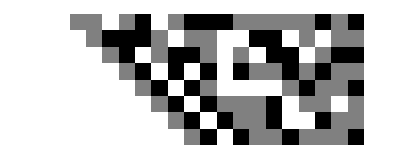

```mathematica
Module[{p=3,a=5,digits=20,rows=10,r=-12},
L31=Table[
Reverse[
IntegerDigits[
PolynomialMod[
CatalanNumber[a*p^n+r]/CatalanNumber[a*p^(n)],p^digits],p,digits]
],
{n,3,rows}];
ArrayPlot[L31]]
```

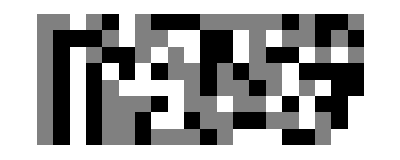

```mathematica
Module[{p=3,a=5,digits=20,rows=10,r=-12},
L31=Table[
Reverse[
IntegerDigits[
PolynomialMod[
(CatalanNumber[a*p^n+r]/CatalanNumber[a*p^(n)]-CatalanNumber[r])/p^(n-1),p^digits],p,digits]
],
{n,3,rows}];
ArrayPlot[L31]]
```

```mathematica
Module[{p=3,a=5,digits=30,rows=25,r=-12},
L31=Table[
Reverse[
IntegerDigits[
PolynomialMod[
CatalanNumber[Fibonacci[n]],p^digits],p,digits]
],
{n,3,rows}];
ArrayPlot[L31]]
```

-Graphics-

```mathematica
Module[{p=2,a=1,digits=19,rows=20},
L33=Table[
PolynomialMod[
CatalanNumber[a*p^rows+r]/CatalanNumber[a*p^(rows)],p^digits],{r,1,15}]]
```

{1,2,262149,14,42,132,131501,263574,267006,16796,320930,208012,218612,53000,323197}

```mathematica
Module[{p=3,a=7,digits=7,rows=10},
L33=Table[
PolynomialMod[
CatalanNumber[a*p^rows+r]/CatalanNumber[a*p^(rows)],p^digits],{r,1,10}]]
```

{1,2,5,14,42,132,429,1430,488,1487}

```mathematica
Table[CatalanNumber[n],{n,1,10}]
```

{1,2,5,14,42,132,429,1430,4862,16796}

```mathematica
Table[CatalanNumber[n],{n,10,20}]
```

{16796,58786,208012,742900,2674440,9694845,35357670,129644790,477638700,1767263190,6564120420}

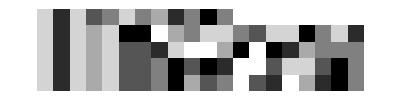

```mathematica
Module[{p=7,a=3,digits=20,rows=5},L30=Table[Reverse[IntegerDigits[PolynomialMod[Fibonacci[p^(2n)],p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L30]]
```

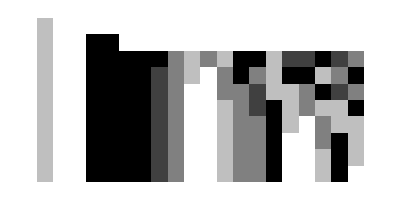

```mathematica
Module[{p=5,a=3,digits=20,rows=10},L30=Table[Reverse[IntegerDigits[PolynomialMod[Fibonacci[p^(n)]/p^n,p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L30]]
```

```mathematica
Catalimit[a_,p_,n_,r_]:=CatalanNumber[r]Binomial[2a,a]Product[PochGamma[1,a*p^i,p],{i,1,a*p^n}]
```

```mathematica
Module[{p=3,a=3,digits=20,rows=10,r=0},L30=Table[Reverse[IntegerDigits[PolynomialMod[Catalimit[a,p,n,r],p^digits],p,digits]],{n,1,rows}];
ArrayPlot[L30]]
```

$Aborted

```mathematica
Module[{p=2,a=1,digits=7,rows=8},
L33=Table[
PolynomialMod[
Catalimit[a,p,rows,r],p^digits],{r,1,10}]]
```

Parallel`Developer`QueueRun::hmm: Received unexpected result SystemException["MemoryAllocationFailure", {"iid"_8[Identity[Product[PochGamma[1, Times[« 2 »], 2], {i, 78, 88, 1}]]], Identity[Product[PochGamma[1, 1\ Power[« 2 »], 2], {i, 78, 88, 1}]], Product[PochGamma[1, 1\ 2^i, 2], {i, 78, 88, 1}], « 46 », Product`FiniteProductDump`res = TimeConstrained[Product`ProductFinitePiecewise[If[Equal[« 2 »], 1, k], {k, 1, 302231454903657293676544}], 10, $Failed], « 94 »}] from KernelObject[1, "local"].

Parallel`Developer`QueueRun::hmm: Received unexpected result SystemException["MemoryAllocationFailure", {"iid"_9[Identity[Product[PochGamma[1, Times[« 2 »], 2], {i, 89, 99, 1}]]], Identity[Product[PochGamma[1, 1\ Power[« 2 »], 2], {i, 89, 99, 1}]], Product[PochGamma[1, 1\ 2^i, 2], {i, 89, 99, 1}], « 46 », Product`FiniteProductDump`res = TimeConstrained[Product`ProductFinitePiecewise[If[Equal[« 2 »], 1, k], {k, 1, 618970019642690137449562112}], 10, $Failed], « 94 »}] from KernelObject[8, "local"].

Parallel`Developer`QueueRun::hmm: Received unexpected result SystemException["MemoryAllocationFailure", {"iid"_7[Identity[Product[PochGamma[1, Times[« 2 »], 2], {i, 67, 77, 1}]]], Identity[Product[PochGamma[1, 1\ Power[« 2 »], 2], {i, 67, 77, 1}]], Product[PochGamma[1, 1\ 2^i, 2], {i, 67, 77, 1}], « 46 », Product`FiniteProductDump`res = TimeConstrained[Product`ProductFinitePiecewise[If[Equal[« 2 »], 1, k], {k, 1, 147573952589676412928}], 10, $Failed], « 94 »}] from KernelObject[2, "local"].

General::stop: Further output of Parallel`Developer`QueueRun :: hmm will be suppressed during this calculation.

$Aborted

```mathematica
Table[CatalanNumber[-n],{n,1,50}]
```

{-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Module[{p=3,a=1,digits=30,rows=15,r=0},
L31=Table[
Reverse[
IntegerDigits[
PolynomialMod[
CatalanNumber[p^n],p^digits],p,digits]
],
{n,3,rows}];
ArrayPlot[L31]]
```

-Graphics-

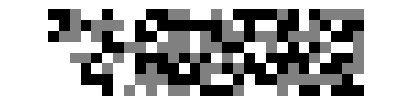

```mathematica
Module[{p=3,a=1,digits=30,rows=10,r=0},
L31=Table[
Reverse[
IntegerDigits[
PolynomialMod[
CatalanNumber[2^(2n)],p^digits],p,digits]
],
{n,3,rows}];
ArrayPlot[L31]]
```

```mathematica
Module[{p=2,a=1,digits=30,rows=15,r=-10},
L31=Table[
Reverse[
IntegerDigits[
PolynomialMod[
3*5*7*9PochGamma[3,a*p^n+r,p],p^digits],p,digits]
],
{n,3,rows}];
ArrayPlot[L31]]
```

-Graphics-

What’s going on with these limits being alternating signed products of odd reciprocals?
Where is the p-adic gamma continuous?